# Pulse Width Modulation

## ...or how to emulate an analog output using a digital signal

## References

https://www.youtube.com/watch?v=YmPziPfaByw

https:// www.arduino.cc/en/Tutorial/PWM

https://learn.sparkfun.com/tutorials/pulse-width-modulation/all

## Why do I need this?

Say you want to modify the speed of a motor or the brightness of an LED. One way to do it would be to modify the voltage applied to it: Less voltage would mean less speed for the motor, and less brightness for the LED since less current flows through it. But most Arduino boards don’t have a way to output varying voltages, they lack a circuit called “DAC” (digital to analog converter). This is where Pulse Width Modulation (PWM) kicks in.

## Let’s learn

So far you’ve learned about the digital input and outputs of an Arduino (or maybe a plain, organic, 100% fat-free microcontroller). You know how to get data into the Arduino and out of it, but only in ones and zeroes. This is great, since we only need ones and zeroes for PWM... we are only going to play with time.

### Square Wave

To understand PWM better, we are first going to break the "waveform" apart.

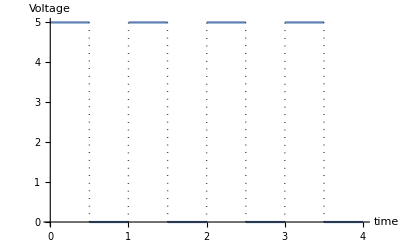

```mathematica
Plot[5 UnitStep[SquareWave[n]], {n,0,4},ExclusionsStyle-> Dotted, AxesLabel->{"time", "Voltage"}]
```

This square wave shows an alternation between 0 a 5 volts.

We see 5 volts for a duration of half a second

We see 0 volts for a duration of half a second

This wave can be read as “a square wave of 1Hz with a 50% duty cycle”.

Hz is the frequency of the wave. 1Hz means 1 cycle per second.

Duty cycle is the portion of time during each cycle where the wave is at 5 volts, also known as “On” time (or HIGH in Arduino). 50% means, of course, that we have 5 volts for half the time and 0 volts for half the time.

If we were to turn and LED on and off with this square wave, we’d get a nice blinking LED. In Arduino code, we could do it with:

void loop() {
	digitalWrite(LED_PIN, HIGH);		// Turn LED on
	delay(500);					// Wait for 500 mS (half a second)
	digitalWrite(LED_PIN, LOW);		// Turn LED off
	delay(500);					// Wait for 500 mS again
}

But what happens when we increase the frequency of this wave? If we go above 60hz, it’d probably be impossible for the human eye to distinguish the flickering (this is called flicker fusion) and it’d seem like the LED is fully ON all the time. 

Play with the wave yourself to see what representing a higher-frequency wave would look like:

```mathematica
Manipulate[
Plot[
5 UnitStep[SquareWave[n*frequency]], {n,0,4},ExclusionsStyle-> Automatic, AxesLabel->{"time", "Voltage"}, Epilog->Inset[Framed[Style[IntegerPart[frequency]"Hz",20]]]], 
{frequency, 1, 10},AppearanceElements->None
]
```

### Pulse Width

Now that we’ve seen what increasing the frequency does, let’s take a look at what changing the duty cycle would do.

```mathematica
pulse[λ_,p_,a_:1][t_]:=If[Mod[t,λ]<λ*p,a,0]
```

```mathematica
pulse[λ_,p_,a_,t_]:=pulse[λ,p,a][t]
```

```mathematica
Manipulate[
Plot[
pulse[2,dutyCycle,5,t],{t,0,5},ExclusionsStyle-> Automatic, AxesLabel->{"time", "Voltage"}, Epilog->Inset[Framed[Style[IntegerPart[dutyCycle*100/1]"%",20]]]
], {dutyCycle, 0.01, 0.9}, AppearanceElements->None ]
```

By changing the duty cycle, you effectively change the time a device is in the ON state. But this has an interesting effect in voltage and current: Their average value is defined by the duty cycle, which means the LED won’t be perceived as blinking, but instead it will be perceived as fading.

You can try this code in Arduino to see it in action:

void loop() {
	for ( int i = 0; i < 255; i++ ) {
		analogWrite( LED_PIN, i );	// Change the PWM value from 0 to 255 (0 being 0% duty cycle, an OFF state, and 255 being a 100% duty cycle, meaning full brightness)
		delay(50);					// Wait 50 mS between steps so you can see the dimming effect
	}
}

### Final Thoughts

With this technique you can control motors, light sources, speakers, peltier-cells, resistor-based heaters and more. Alternating the width in different periods can also be used as a means of communication (i.e. to control the angle of a hobby-servo motor), or you can feed an h-bridge to alter the speed of a dc or stepper motors.
This technique is also used in switching power supplies such as buck converters and boost converters.